```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/J2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

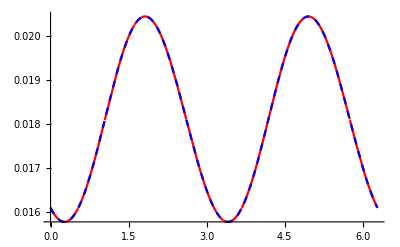

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression -(ⅈ (0.+0. ⅈ) ComplexInfinity)/(4 π) encountered.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

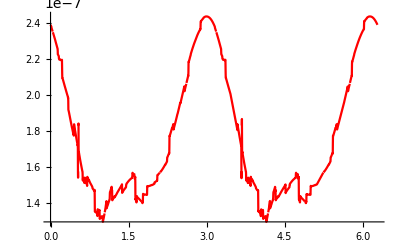

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1,{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

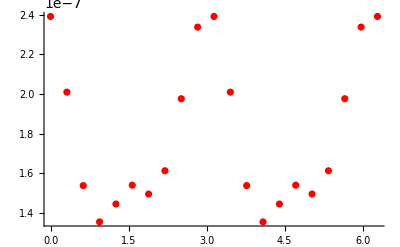

```mathematica
ListPlot[Table[{ϕ,J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1},{ϕ,0,2π,0.1π}],PlotStyle->{{Red},{Blue,Dashed}}]
```

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u},
x2u=-x1u;x4u=-x3u;
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
Print["v_2=",NIntegrate[dσ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]];
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]
]
```

### b = 0, kT = 1.0

InterpolatingFunction::dmval: Input value {-1.,-15.0003} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

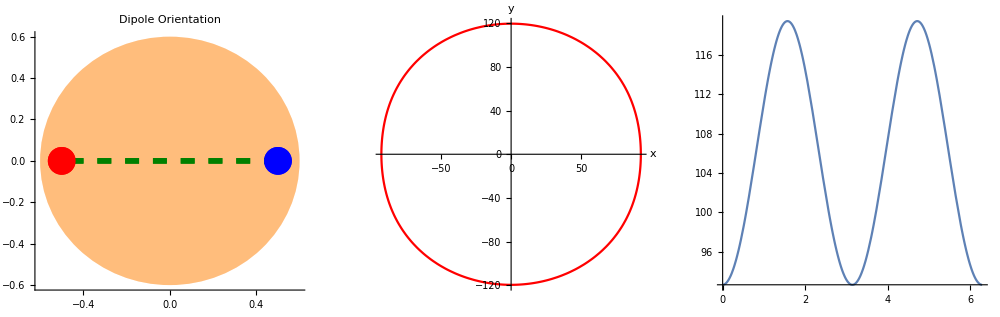

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$10344689 near {ϕ$10344689} = {1.70569}. NIntegrate obtained -1.33227×10^-15 and 2.94376×10^-12 for the integral and error estimates.

{-0.0633491,-2.00522×10^-18}

```mathematica
x1u={1/2,0};
x3u={1/2,0};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

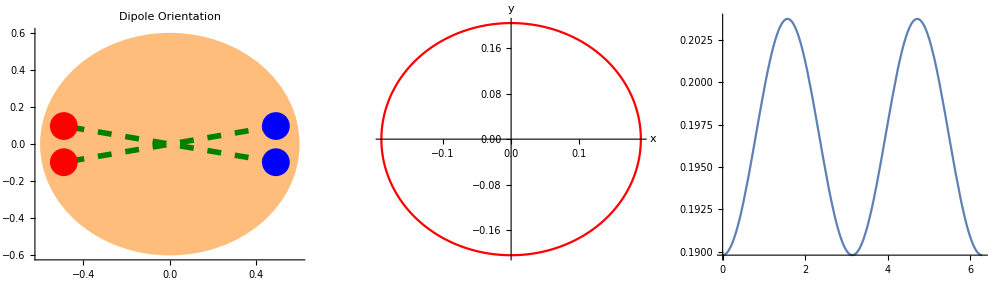

{-0.0177289,2.82249×10^-8}

{-0.0177289,2.82249×10^-8}

```mathematica
θ=π/16;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
showdσHZ[bu,x1u,x3u,kT,False]
```

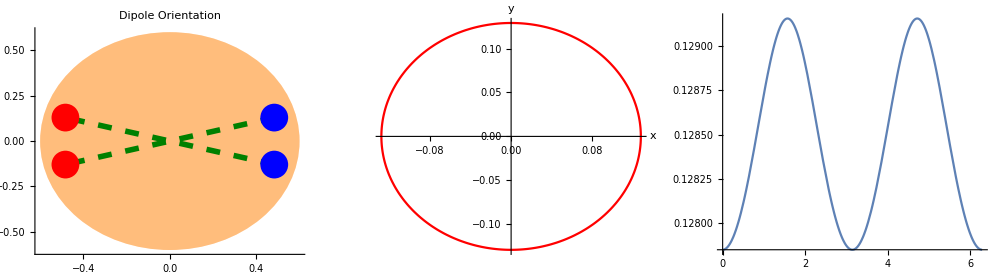

{-0.00254539,3.60683×10^-8}

```mathematica
θ=π/12;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

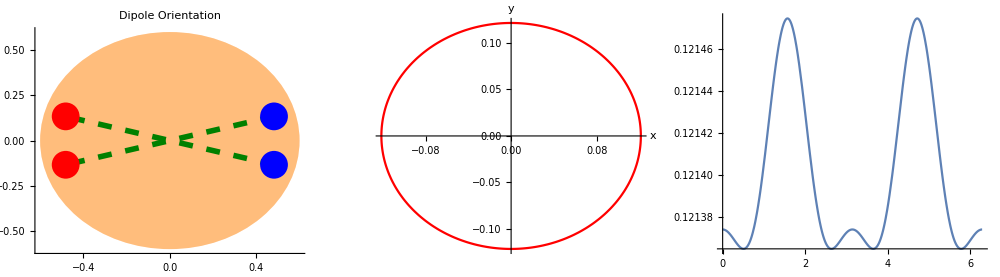

{-0.000204641,6.48675×10^-8}

```mathematica
θ=π/11.6;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

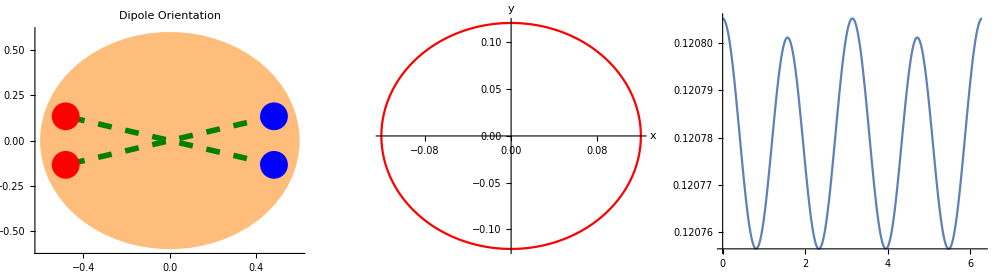

{0.0000110804,6.6607×10^-8}

```mathematica
θ=π/11.565;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

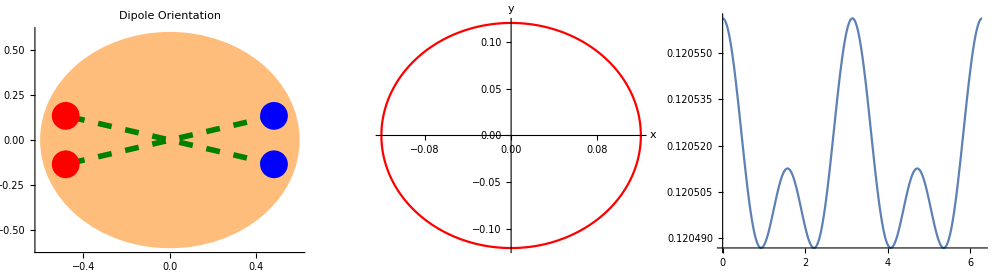

{0.000104099,6.73066×10^-8}

```mathematica
θ=π/11.55;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

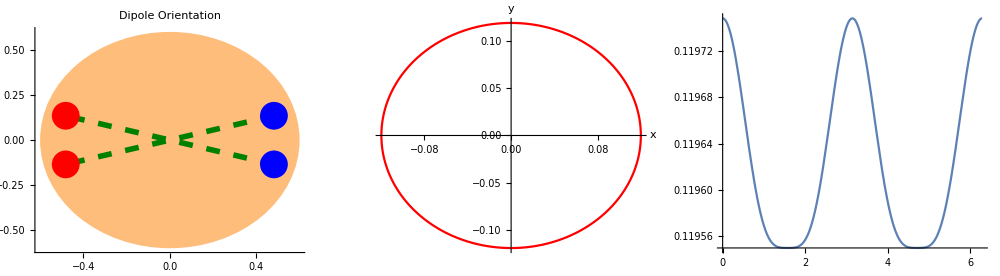

{0.000416641,6.94326×10^-8}

```mathematica
θ=π/11.5;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

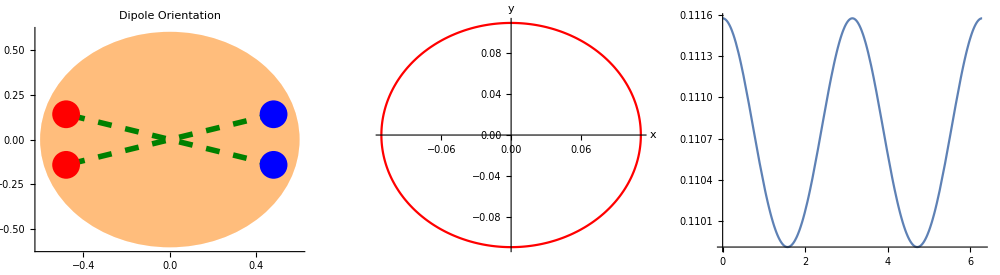

{0.0037672,7.01327×10^-8}

```mathematica
θ=π/11;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

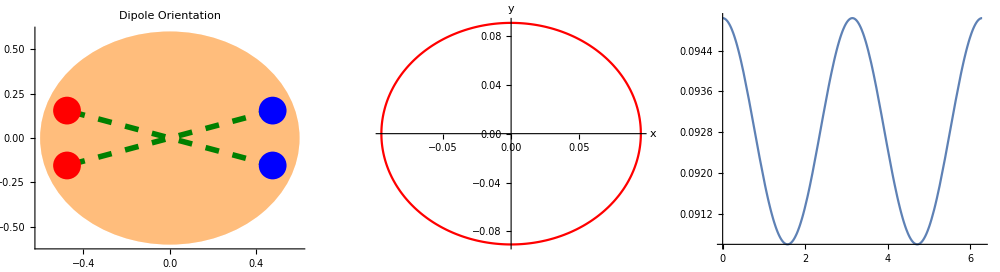

{0.0119718,4.14811×10^-8}

```mathematica
θ=π/10;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

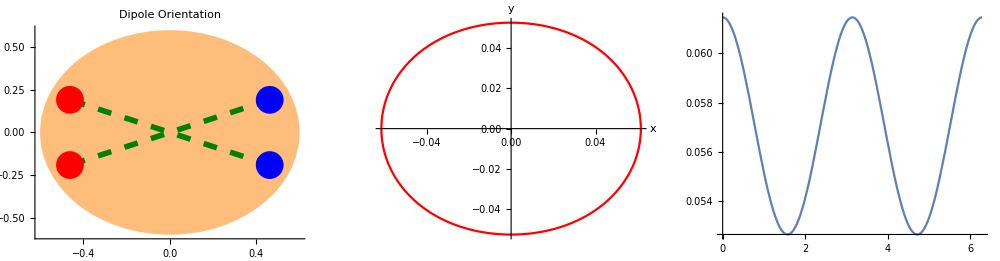

{0.0385892,5.356×10^-8}

```mathematica
θ=π/8;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

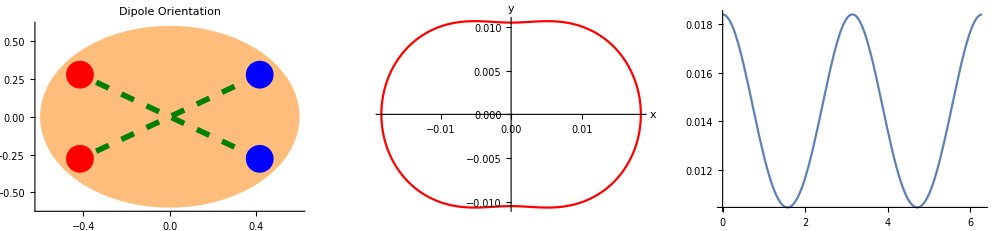

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$6856288 near {ϕ$6856288} = {6.0340560481230842426736415973209659568965435028076171875}. NIntegrate obtained -2.37721×10^-9 and 2.92058×10^-13 for the integral and error estimates.

{0.138345,-2.64589×10^-8}

```mathematica
θ=(3π)/16;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

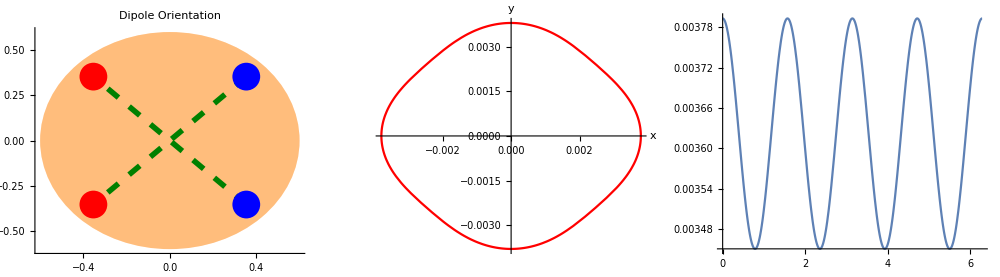

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7038328 near {ϕ$7038328} = {4.71229}. NIntegrate obtained -9.21572×10^-19 and 2.0574×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7038328 near {ϕ$7038328} = {2.95742}. NIntegrate obtained -1.42275×10^-9 and 1.50031×10^-13 for the integral and error estimates.

{-4.04974×10^-17,-6.25213×10^-8}

```mathematica
θ=π/4;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

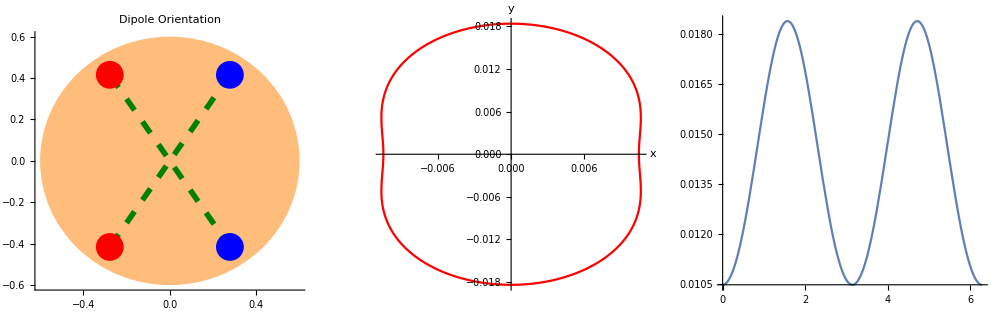

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$7318653 near {ϕ$7318653} = {3.30103}. NIntegrate obtained -2.35215×10^-9 and 2.24338×10^-13 for the integral and error estimates.

{-0.138345,-2.618×10^-8}

```mathematica
θ=(5π)/16;
x1u=1/2{Cos[θ],Sin[θ]};
x3u=1/2{Cos[-θ],Sin[-θ]};
bu={10^-15,0};
kT=1.0;
showdσHZ[bu,x1u,x3u,kT]
```

```mathematica
v2b0=Table[{2 ϕ/π,
showdσHZ[{10^-15,0},1/2{Cos[ϕ],Sin[ϕ]},1/2{Cos[-ϕ],Sin[-ϕ]},1.0,False][[1]]},{ϕ,0,π/2,π/(2*100)}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$10544523 near {ϕ$10544523} = {1.70569}. NIntegrate obtained -1.33227×10^-15 and 2.94376×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$10601491 near {ϕ$10601491} = {4.58957}. NIntegrate obtained -1.71568×10^-11 and 4.36288×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$10658447 near {ϕ$10658447} = {1.44798}. NIntegrate obtained -8.84074×10^-11 and 4.46552×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0,-0.0633491},{1/200,-0.050048},{1/100,-0.0467814},{3/200,-0.0440411},{1/50,-0.0414763},{1/40,-0.0389593},{3/100,-0.0364261},{7/200,-0.0338381},{1/25,-0.0311695},{9/200,-0.0284013},{1/20,-0.0255183},{11/200,-0.0225077},{3/50,-0.0193586},{13/200,-0.0160608},{7/100,-0.0126048},{3/40,-0.00898139},{2/25,-0.00518134},{17/200,-0.00119559},{9/100,0.00298531},{19/200,0.0073711},{1/10,0.0119718},{21/200,0.0167979},{11/100,0.0218608},{23/200,0.027172},{3/25,0.0327438},{1/8,0.0385892},{13/100,0.0447217},{27/200,0.0511549},{7/50,0.0579025},{29/200,0.064978},{3/20,0.0723931},{31/200,0.0801574},{4/25,0.0882761},{33/200,0.096747},{17/100,0.105557},{7/40,0.114675},{9/50,0.124045},{37/200,0.13357},{19/100,0.143095},{39/200,0.152382},{1/5,0.161067},{41/200,0.168617},{21/100,0.174264},{43/200,0.176945},{11/50,0.175259},{9/40,0.167494},{23/100,0.151823},{47/200,0.126747},{6/25,0.0918165},{49/200,0.0484009},{1/4,-4.04974×10^-17},{51/200,-0.0484009},{13/50,-0.0918165},{53/200,-0.126747},{27/100,-0.151823},{11/40,-0.167494},{7/25,-0.175259},{57/200,-0.176945},{29/100,-0.174264},{59/200,-0.168617},{3/10,-0.161067},{61/200,-0.152382},{31/100,-0.143095},{63/200,-0.13357},{8/25,-0.124045},{13/40,-0.114675},{33/100,-0.105557},{67/200,-0.096747},{17/50,-0.0882761},{69/200,-0.0801574},{7/20,-0.0723931},{71/200,-0.064978},{9/25,-0.0579025},{73/200,-0.0511549},{37/100,-0.0447217},{3/8,-0.0385892},{19/50,-0.0327438},{77/200,-0.027172},{39/100,-0.0218608},{79/200,-0.0167979},{2/5,-0.0119718},{81/200,-0.0073711},{41/100,-0.00298531},{83/200,0.0011956},{21/50,0.00518134},{17/40,0.00898139},{43/100,0.0126048},{87/200,0.0160608},{11/25,0.0193586},{89/200,0.0225077},{9/20,0.0255183},{91/200,0.0284013},{23/50,0.0311695},{93/200,0.0338381},{47/100,0.0364261},{19/40,0.0389593},{12/25,0.0414763},{97/200,0.0440411},{49/100,0.0467814},{99/200,0.050048},{1/2,0.063349}}

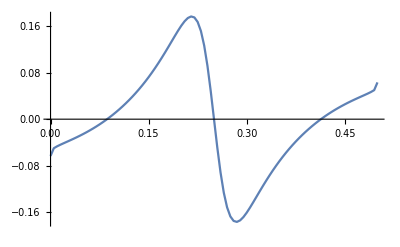

```mathematica
ListPlot[v2b0,Joined->True]
```

### b != 0

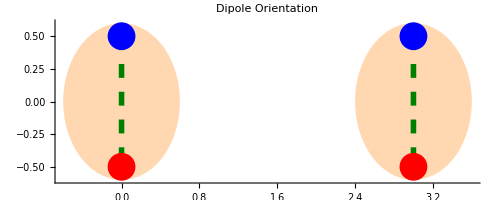

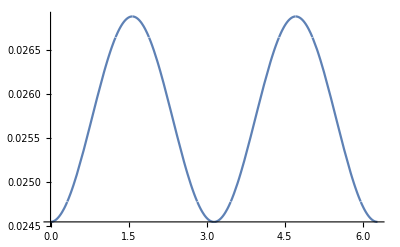

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1364063 near {ϕ$1364063} = {0.0000241858}. NIntegrate obtained -2.4091×10^-16+0. ⅈ and 2.11759×10^-16 for the integral and error estimates.

v_2={-0.0226608+0. ⅈ,-1.49165×10^-15+0. ⅈ}

```mathematica
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

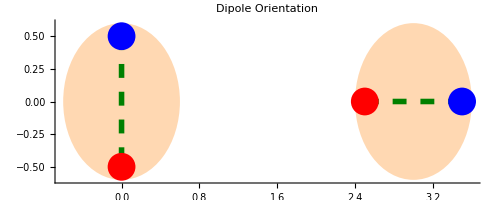

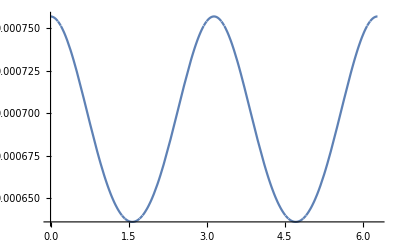

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1569161 near {ϕ$1569161} = {5.49769}. NIntegrate obtained -3.66664×10^-17-1.17726×10^-20 ⅈ and 2.0624×10^-17 for the integral and error estimates.

v_2={0.043477,-8.41336×10^-15-2.7013×10^-18 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

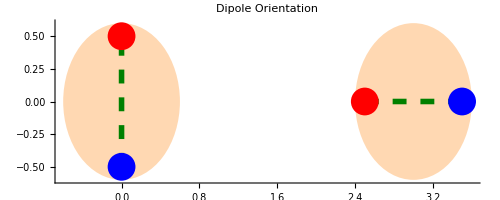

-Graphics-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1799031 near {ϕ$1799031} = {5.49769}. NIntegrate obtained -3.66664×10^-17-1.17726×10^-20 ⅈ and 2.0624×10^-17 for the integral and error estimates.

v_2={0.043477,-8.41336×10^-15-2.7013×10^-18 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{Cos[π/2],Sin[π/2]};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

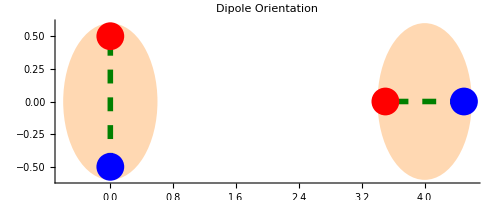

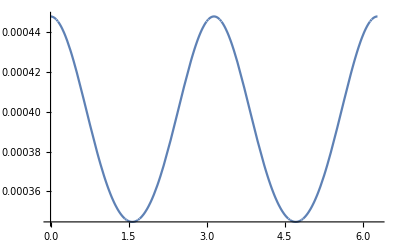

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2028901 near {ϕ$2028901} = {3.95144}. NIntegrate obtained 1.17907×10^-17-3.46982×10^-21 ⅈ and 1.17273×10^-17 for the integral and error estimates.

v_2={0.0654057,4.76983×10^-15-1.40369×10^-18 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{Cos[π/2],Sin[π/2]};
bu={4,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

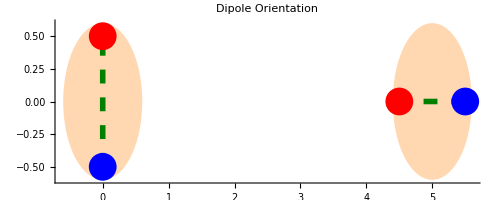

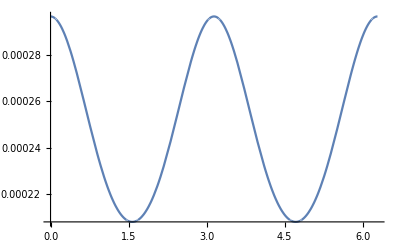

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2229257 near {ϕ$2229257} = {2.46654}. NIntegrate obtained -1.59666×10^-18+2.45713×10^-21 ⅈ and 8.34485×10^-18 for the integral and error estimates.

v_2={0.0888849,-1.0177×10^-15+1.56615×10^-18 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{Cos[π/2],Sin[π/2]};
bu={5,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

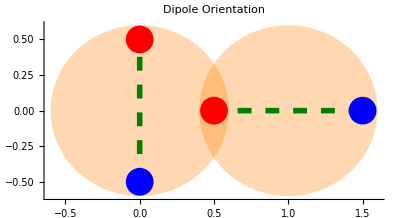

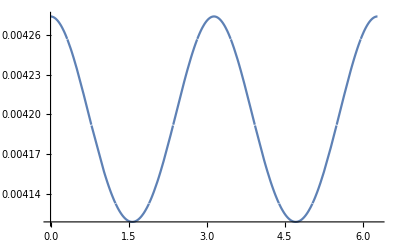

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2445489 near {ϕ$2445489} = {3.9269908451597596520323736587854910598180402381274234357988461852}. NIntegrate obtained -8.5713×10^-17-1.90359×10^-21 ⅈ and 1.99157×10^-15 for the integral and error estimates.

v_2={0.00924929,-3.25259×10^-15-7.22365×10^-20 ⅈ}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```

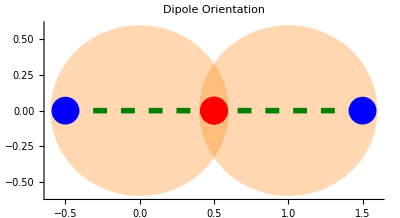

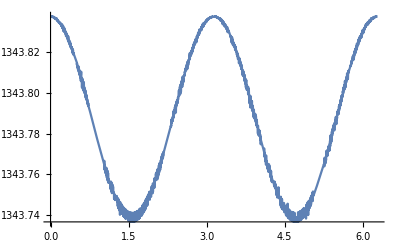

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2768168 near {ϕ$2768168} = {1.75483}. NIntegrate obtained 0.155546+0. ⅈ and 0.00025907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2768168 near {ϕ$2768168} = {0.871252}. NIntegrate obtained 0.00074612+0. ⅈ and 0.000284675 for the integral and error estimates.

v_2={0.0000184224,8.83686×10^-8}

```mathematica
x1u=1/2{1,0};
x3u=-1/2{1+10^-10,0};
bu={1,0};
kT=0.1;
showdσ[bu,x1u,x3u,kT]
```